```mathematica
(*Part 2*)
```

```mathematica
Subscript[k, o]=a
```

```mathematica
σ
```

σ

```mathematica
ψ[k_]:=1/(√(2 σ^2 π))e^(-(k-a)^2/(2 σ^2))
```

```mathematica
FourierTransform[Exp[(-(k-a)^2/(2*σ^2))]*(1/√(2*σ^2*π)),k,x]
```

(ⅇ^(ⅈ a x-(x^2 σ^2)/2) √(1/σ^2) √(σ^2))/(√(2 π))

```mathematica
(*Part 3*)
```

```mathematica
a=0
```

0

```mathematica
σ=1
```

1

```mathematica
FourierTransform[Exp[(-(k-a)^2/(2*σ^2))]*(1/√(2*σ^2*π)),k,x]
```

(ⅇ^(-x^2/2))/(√(2 π))

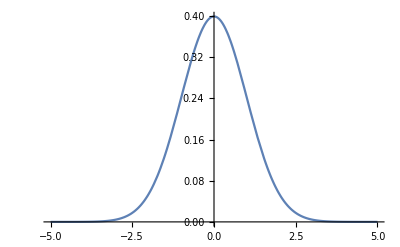

```mathematica
Plot[Abs[(ⅇ^(-x^2/2))/(√(2 π))],{x,-5,5}]
```